```mathematica
S[x_,n_]:=Sqrt[(n-1)/n+x x/n]
DHC5[x_,n_,Kp_,sn_]:=sn(1/Sqrt[n(n+1)]x+(S[x,n]-1)Kp)
DAF[x_,n_,Kp_,sn_,kn_,knn_]:=sn(S[x,n](Kp+knn)-(Kp+kn))
DPNEC[x_,n_,Kp_,sn_,kn_,knn_]:=DHC5[x,n,Kp,sn]-DAF[x,n,Kp,sn,kn,knn]
```

## Sn Ratio

10

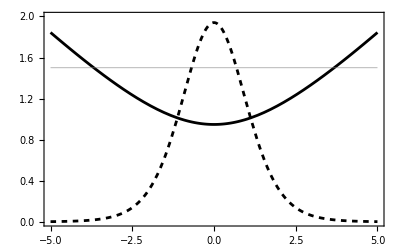

```mathematica
SS=10 (* sample size *)
ai=Plot[S[x,SS],{x,-5,5},PlotStyle->GrayLevel[0],PlotRange->{0,2},Frame->True];
bi=Plot[5PDF[StudentTDistribution[SS-1],x],{x,-5,5},PlotStyle->{Dashing[{0.01,0.01}],GrayLevel[0]},Frame->True];
ci=Plot[1.5,{x,-5,5},PlotStyle->{GrayLevel[0.5],Thickness[0.001]}];
Show[ai,bi,ci]
```

### intersections between curves and z (=log10(v))

```mathematica
solX=Solve[S[x,n]==z,x]
minSn = S[0,n]
```

{{x→-√(1-n+n z^2)},{x→√(1-n+n z^2)}}

√((-1+n)/n)

if z < minSn, then there are no intersections. For example, when SS = 10, minSn is 0.948683 (snn will never be lower than 0.95 sn). Horizontal gray line has no intersections with thick curve for S(x)

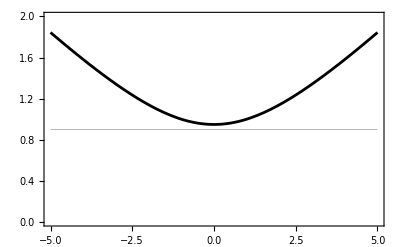

```mathematica
ai=Plot[S[x,SS],{x,-5,5},PlotStyle->GrayLevel[0],PlotRange->{0,2},Frame->True];
bi=Plot[0.9,{x,-5,5},PlotStyle->{GrayLevel[0.5],Thickness[0.001]}];
Show[ai,bi]
```

### CDF

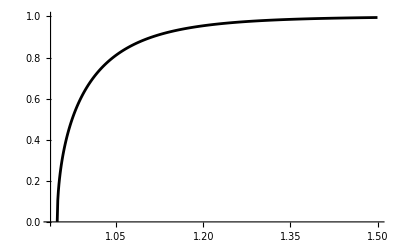

```mathematica
SS=10;
minSn = S[0,n];
del=0.001;
intRng=x/.solX/.n->SS;
znow=minSn/.n->SS;
myCDF={{znow,0}};

Do[
znow=znow+del;
If[znow>1.5, Break[]];
xl=intRng[[1]]/.z->znow;
xh=-xl;
p=CDF[StudentTDistribution[SS-1],xh]-CDF[StudentTDistribution[SS-1],xl];
AppendTo[myCDF,{znow,p}];
,{k,10000}];
grCDF=ListPlot[myCDF,Joined->True,PlotRange->{0,1},PlotStyle->{Thickness[0.005],GrayLevel[0]}]
```

### PDF

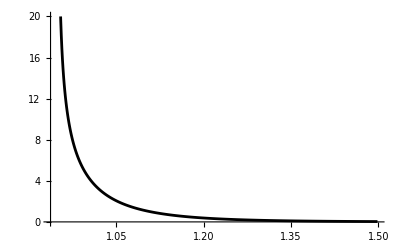

```mathematica
ya=Transpose[myCDF][[2]];
xa=Transpose[myCDF][[1]];
myPDF={};
Do[
AppendTo[myPDF,{xa[[k]],(ya[[k+1]]-ya[[k]])/(xa[[k+1]]-xa[[k]])}];
,{k,Length[myCDF]-1}];
grPDF=ListPlot[myPDF,Joined->True,PlotRange->{0,20},PlotStyle->{Thickness[0.005],GrayLevel[0]}]
```

### comparison with monte-carlo

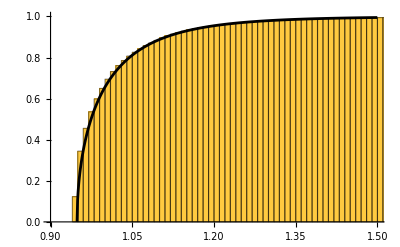

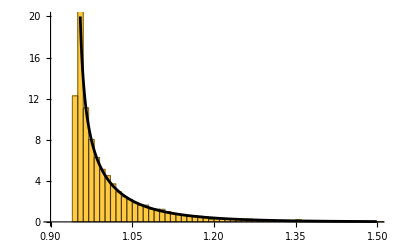

```mathematica
snRatios={};
Do[
preSample=Table[RandomReal[NormalDistribution[0,3.14]],{k,10}];
preSd=StandardDeviation[preSample];

postSample=AppendTo[preSample,RandomReal[NormalDistribution[0,3.14]]];
postSd=StandardDeviation[postSample];

sRatio=postSd/preSd;
AppendTo[snRatios,sRatio];
,{t,10000}];
ci=Histogram[snRatios,100,"CDF"];
di=Histogram[snRatios,100,"PDF"];
Show[ci,grCDF,PlotRange->{{0.9,1.5},{0,1}},AxesOrigin->{0.9,0}]
Show[di,grPDF,PlotRange->{{0.9,1.5},{0,20}},AxesOrigin->{0.9,0}]
```

## change in HC5

```mathematica
K5=Quantile[NormalDistribution[0,1],0.05]
```

-1.64485

### functional form of dlogHC5. sn = 0.5 and 1.5, as example

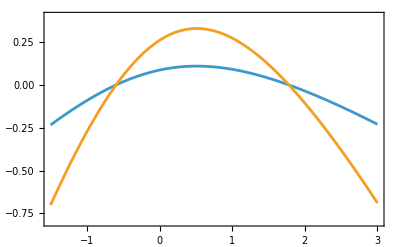

```mathematica
SS=5;
Plot[Evaluate[{DHC5[x,SS,K5,0.5],DHC5[x,SS,K5,1.5]}],{x,-1.5,3},Frame->True,PlotRange->{-0.8,0.4}]
```

### obtaining the probability that post-HC5 > v pre-HC5 (z = log10(v)). n=5, v = 2, sn=1.5 as example

```mathematica
solX=FullSimplify[x/.Solve[DHC5[x,n,Kp,sn]==z,x]]
maxX=FullSimplify[x/.Solve[D[DHC5[x,n,Kp,sn],x]==0,x][[2]]]
maxHC5=FullSimplify[DHC5[maxX,n,Kp,sn]]

SS=5; 
params={Kp->K5,n->SS,sn->1.5};
If[(maxHC5/.params)<Log10[2],Print["No solution"]]
intRng=solX/.params/.z->Log10[2];
Print["Probability that post-HC5 > 2 pre-HC5"]
(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]])
```

{-(√(n (1+n)) sn (Kp sn+z)+√(Kp^2 (1+n) sn^2 ((-1+n+Kp^2 (1+n)) sn^2+2 Kp n (1+n) sn z+n (1+n) z^2)))/((-1+Kp^2 (1+n)) sn^2),(-√(n (1+n)) sn (Kp sn+z)+√(Kp^2 (1+n) sn^2 ((-1+n+Kp^2 (1+n)) sn^2+2 Kp n (1+n) sn z+n (1+n) z^2)))/((-1+Kp^2 (1+n)) sn^2)}

(√(-1+n))/(√(-1+Kp^2 (1+n)))

((√(-1+n))/(√(n (1+n)) √(-1+Kp^2 (1+n)))+Kp (-1+√((Kp^2 (-1+n^2))/(n (-1+Kp^2 (1+n)))))) sn

Probability that post-HC5 > 2 pre-HC5

0.212828

### CDF of delta log HC5, sn=1, n=5 as example ( probabilities that post-HC5 is lower than pre-HC5)

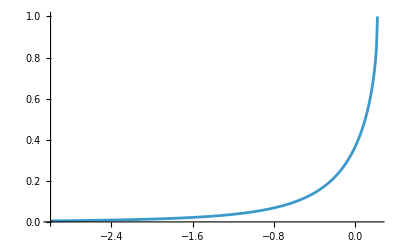

```mathematica
SS=5; 
params={Kp->K5,n->SS,sn->1};
maxZ=maxHC5/.params;
del=0.01;
znow=-3;
myCDF={};
Do[
intRng=solX/.params/.z->znow;
If[znow>maxZ,Break[]];
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
AppendTo[myCDF,{znow,1-p}];
znow=znow+del;
,{k,100000}]
myCDF=AppendTo[myCDF,{maxZ,1}];
grCDF=ListPlot[myCDF,Joined->True,PlotRange->All,AxesOrigin->{-3,0}]
```

### PDF

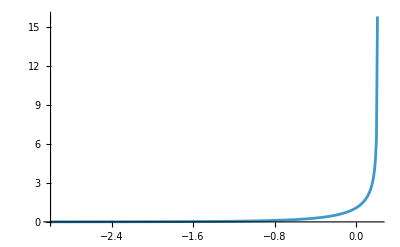

```mathematica
ya=Transpose[myCDF][[2]];
xa=Transpose[myCDF][[1]];
myPDF={};
Do[
AppendTo[myPDF,{xa[[k]],(ya[[k+1]]-ya[[k]])/(xa[[k+1]]-xa[[k]])}];
,{k,Length[myCDF]-1}];
grPDF=ListPlot[myPDF,Joined->True,PlotRange->All,AxesOrigin->{-3,0}]
```

### comparison with monte-carlo

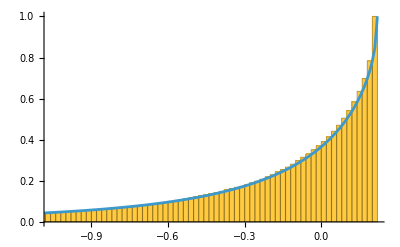

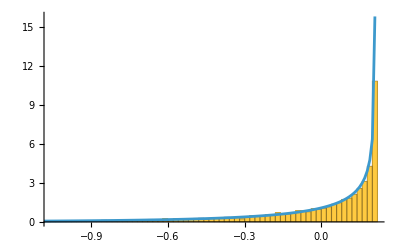

```mathematica
dHC5s={};
Do[
preSample=Table[RandomReal[NormalDistribution[0,3.14]],{k,SS}];
preSd=StandardDeviation[preSample];
preMean=Mean[preSample];
preHC5 = preMean+K5 preSd;

postSample=AppendTo[preSample,RandomReal[NormalDistribution[0,3.14]]];
postSd=StandardDeviation[postSample];
postMean=Mean[postSample];
postHC5 = postMean+K5 postSd;

dHC5=(postHC5-preHC5)/preSd;
AppendTo[dHC5s,dHC5];
,{t,10000}];
ci=Histogram[dHC5s,500,"CDF"];
di=Histogram[dHC5s,500,"PDF"];
Show[ci,grCDF]
Show[di,grPDF]
```

### dependencies of sn on the probability that postHC5 > preHC5

{1.37027,0.801557,0.01,0.01,0.01,0.01}

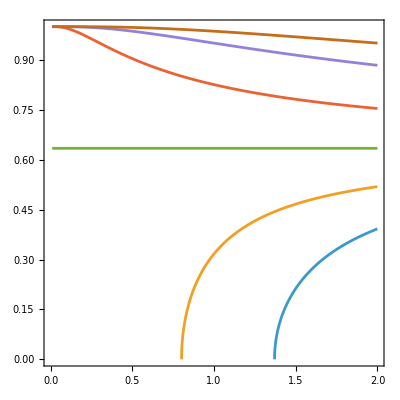

```mathematica
SS=5; 
params={Kp->K5,n->SS};
del=0.001;
minSn = sn/.Solve[maxHC5==z,sn][[1]];
vs=Log10[{2,1.5,1,0.5,0.1,0.01}];
mins={};
Do[
snnow=minSn/.params/.z->vs[[k]];
If[snnow<0.01,AppendTo[mins,0.01],AppendTo[mins,snnow]];
,{k,Length[vs]}];
mins
grs={};
Do[
snnow=mins[[k]];
dHC5s={};
Do[
If[snnow>2.0,Break[]];
intRng=solX/.params/.z->vs[[k]]/.sn->snnow;
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
AppendTo[dHC5s,{snnow,p}];
snnow=snnow+del;
,{t,10000}];
If[Length[dHC5s]>0,AppendTo[grs,dHC5s]];
,{k,Length[vs]}];
ListPlot[grs,Joined->True,AspectRatio->1,Frame->True,PlotRange->{{0,2},{0,1}}]
```

{2.71568,1.58857,0.01,0.01,0.01,0.01}

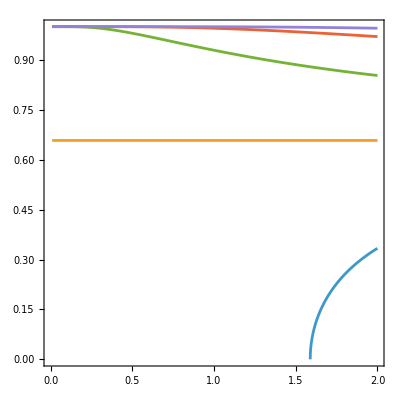

```mathematica
SS=10; 
params={Kp->K5,n->SS};
del=0.001;
minSn = sn/.Solve[maxHC5==z,sn][[1]];
vs=Log10[{2,1.5,1,0.5,0.1,0.01}];
mins={};
Do[
snnow=minSn/.params/.z->vs[[k]];
If[snnow<0.01,AppendTo[mins,0.01],AppendTo[mins,snnow]];
,{k,Length[vs]}];
mins
grs={};
Do[
snnow=mins[[k]];
dHC5s={};
Do[
If[snnow>2.0,Break[]];
intRng=solX/.params/.z->vs[[k]]/.sn->snnow;
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
AppendTo[dHC5s,{snnow,p}];
snnow=snnow+del;
,{t,10000}];
If[Length[dHC5s]>0,AppendTo[grs,dHC5s]];
,{k,Length[vs]}];
ListPlot[grs,Joined->True,AspectRatio->1,Frame->True,PlotRange->{{0,2},{0,1}}]
```

## Change in AF

{Kp→-1.64485,n→5,sn→1,kn→4.20268,knn→3.70768}

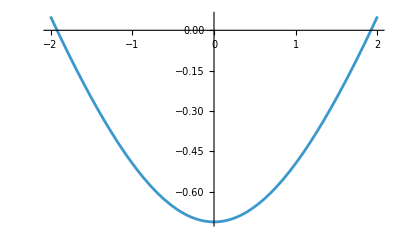

{-1/(√(knn^2+2 knn Kp+Kp^2) sn)(√(knn^2 sn^2+2 knn Kp sn^2+Kp^2 sn^2+kn^2 n sn^2-knn^2 n sn^2+2 kn Kp n sn^2-2 knn Kp n sn^2+2 kn n sn z+2 Kp n sn z+n z^2)),1/(√(knn^2+2 knn Kp+Kp^2) sn)(√(knn^2 sn^2+2 knn Kp sn^2+Kp^2 sn^2+kn^2 n sn^2-knn^2 n sn^2+2 kn Kp n sn^2-2 knn Kp n sn^2+2 kn n sn z+2 Kp n sn z+n z^2))}

Probability that AF increases

0.12723

```mathematica
SS=5;
params={Kp->K5,n->SS,sn->1,kn->Quantile[NoncentralStudentTDistribution[SS-1,-Sqrt[SS]K5],0.95]/Sqrt[SS],
knn->Quantile[NoncentralStudentTDistribution[SS,-Sqrt[SS+1]K5],0.95]/Sqrt[SS+1]}
Plot[DAF[x,SS,Kp,sn,kn,knn]/.params,{x,-2,2}]
solX=x/.Solve[DAF[x,n,Kp,sn,kn,knn]==z,x]
minAF=DAF[0,n,Kp,sn,kn,knn];

Print["Probability that AF increases"]
intRng=solX/.params/.z->0;
p=1-(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]])
```

### CDF

-0.712775

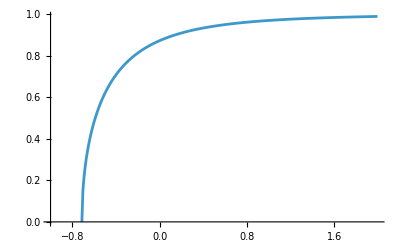

```mathematica
params={Kp->K5,n->SS,sn->1,kn->Quantile[NoncentralStudentTDistribution[SS-1,-Sqrt[SS]K5],0.95]/Sqrt[SS],
knn->Quantile[NoncentralStudentTDistribution[SS,-Sqrt[SS+1]K5],0.95]/Sqrt[SS+1]};
del=0.01;
AFnow=minAF/.params
myCDF={{AFnow,0}};
Do[
AFnow=AFnow+del;
If[AFnow>2,Break[]];
intRng=solX/.params/.z->AFnow;
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
AppendTo[myCDF,{AFnow,p}];
,{k,100000}];
grCDF=ListPlot[myCDF,Joined->True,PlotRange->All,AxesOrigin->{-1,0}]
```

### comparison with monte-carlo

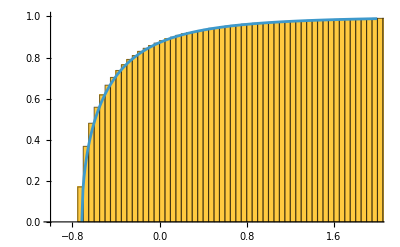

```mathematica
dAFs={};
Do[
preSample=Table[RandomReal[NormalDistribution[0,3.14]],{k,SS}];
preSd=StandardDeviation[preSample];
preAF=preSd(Kp+kn)/.params;

postSample=AppendTo[preSample,RandomReal[NormalDistribution[0,3.14]]];
postSd=StandardDeviation[postSample];
postAF=postSd(Kp+knn)/.params;

dAF=(postAF-preAF)/preSd;
AppendTo[dAFs,dAF];
,{t,10000}];
ci=Histogram[dAFs,200,"CDF"];
Show[ci,grCDF,PlotRange->{{-1,2},All},AxesOrigin->{-1,0}]
```

## change in PNEC

{Kp→-1.64485,n→5,sn→1,kn→4.20268,knn→3.70768}

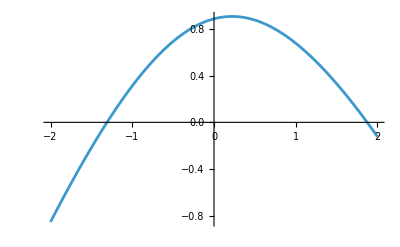

{1/(2 (-1+knn^2+knn^2 n) sn^2)(-√(n (1+n)) sn (-2 kn sn+2 z)-√(n (1+n) sn^2 (-2 kn sn+2 z)^2-4 (-1+knn^2+knn^2 n) sn^2 (-knn^2 sn^2-kn^2 n sn^2-kn^2 n^2 sn^2+knn^2 n^2 sn^2+2 kn n sn z+2 kn n^2 sn z-n z^2-n^2 z^2))),1/(2 (-1+knn^2+knn^2 n) sn^2)(-√(n (1+n)) sn (-2 kn sn+2 z)+√(n (1+n) sn^2 (-2 kn sn+2 z)^2-4 (-1+knn^2+knn^2 n) sn^2 (-knn^2 sn^2-kn^2 n sn^2-kn^2 n^2 sn^2+knn^2 n^2 sn^2+2 kn n sn z+2 kn n^2 sn z-n z^2-n^2 z^2)))}

(√(-1+n))/(√(-1+knn^2 (1+n)))

-((-kn-Kp+(knn+Kp) √((-1+n)/n+(-1+n)/(n (-1+knn^2 (1+n))))) sn)+((√(-1+n))/(√(n (1+n)) √(-1+knn^2 (1+n)))+Kp (-1+√((-1+n)/n+(-1+n)/(n (-1+knn^2 (1+n)))))) sn

Probability that PNEC increases

0.802623

```mathematica
SS=5;
params={Kp->K5,n->SS,sn->1,kn->Quantile[NoncentralStudentTDistribution[SS-1,-Sqrt[SS]K5],0.95]/Sqrt[SS],
knn->Quantile[NoncentralStudentTDistribution[SS,-Sqrt[SS+1]K5],0.95]/Sqrt[SS+1]}
Plot[DPNEC[x,SS,Kp,sn,kn,knn]/.params,{x,-2,2}]
solX=x/.Solve[DPNEC[x,n,Kp,sn,kn,knn]==z,x]
maxX=x/.Simplify[Solve[D[DPNEC[x,n,Kp,sn,kn,knn],x]==0,x][[2]]]
maxPNEC=DPNEC[maxX,n,Kp,sn,kn,knn]

Print["Probability that PNEC increases"]
intRng=solX/.params/.z->0;
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]])
```

### CDF

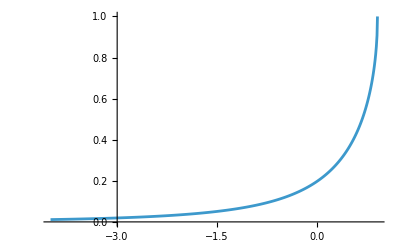

```mathematica
SS=5; 
params={Kp->K5,n->SS,sn->1,kn->Quantile[NoncentralStudentTDistribution[SS-1,-Sqrt[SS]K5],0.95]/Sqrt[SS],
knn->Quantile[NoncentralStudentTDistribution[SS,-Sqrt[SS+1]K5],0.95]/Sqrt[SS+1]};
maxZ=maxPNEC/.params;
del=0.01;
znow=-4;
myCDF={};
Do[
intRng=solX/.params/.z->znow;
If[znow>maxZ,Break[]];
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
AppendTo[myCDF,{znow,1-p}];
znow=znow+del;
,{k,100000}]
myCDF=AppendTo[myCDF,{maxZ,1}];
grCDF=ListPlot[myCDF,Joined->True,PlotRange->All,AxesOrigin->{-3,0}]
```

### comparison with monte-carlo

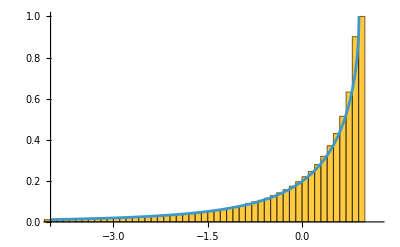

```mathematica
dPNECs={};
Do[
preSample=Table[RandomReal[NormalDistribution[0,3.14]],{k,SS}];
preMean=Mean[preSample];
preSd=StandardDeviation[preSample];
preNOEC=preMean-(kn preSd/.params);

postSample=AppendTo[preSample,RandomReal[NormalDistribution[0,3.14]]];
postMean=Mean[postSample];
postSd=StandardDeviation[postSample];
postNOEC=postMean-(knn postSd/.params);

dPNEC=(postNOEC-preNOEC)/preSd;
AppendTo[dPNECs,dPNEC];
,{t,10000}];
ci=Histogram[dPNECs,200,"CDF"];
Show[ci,grCDF,PlotRange->{{-4,1.2},All},AxesOrigin->{-4,0}]
```

### dependencies of sn on the probability that postPNEC > v prePNEC

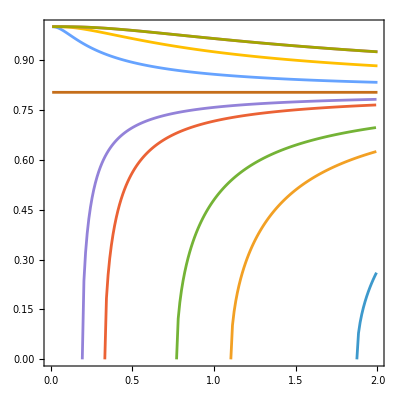

```mathematica
SS=5; 
params={Kp->K5,n->SS,kn->Quantile[NoncentralStudentTDistribution[SS-1,-Sqrt[SS]K5],0.95]/Sqrt[SS],
knn->Quantile[NoncentralStudentTDistribution[SS,-Sqrt[SS+1]K5],0.95]/Sqrt[SS+1]};
del=0.01;
minSn = sn/.Solve[maxPNEC==z,sn][[1]];
snnow=minSn/.params/.z->vs[[2]];

vs=Log10[{50,10,5,2,1.5,1,0.5,0.1,0.01,0.01}];

mins={};
Do[
snnow=minSn/.params/.z->vs[[k]];
If[snnow<0.01,AppendTo[mins,0.01],AppendTo[mins,snnow]];
,{k,Length[vs]}];
grs={};
Do[
snnow=mins[[k]];
dPNECs={};
Do[
If[snnow>2.0,Break[]];
intRng=solX/.params/.z->vs[[k]]/.sn->snnow;
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
AppendTo[dPNECs,{snnow,p}];
snnow=snnow+del;
,{t,10000}];
If[Length[dPNECs]>0,AppendTo[grs,dPNECs]];
,{k,Length[vs]}];
ListPlot[grs,Joined->True,AspectRatio->1,Frame->True,PlotRange->{{0,2},{0,1}}]
```

## Values of sn for which P(post-HC5 <.bd× or >2× pre-HC5) = 0.05

This involves finding the intersection of the wavy line and the curve in the diagram below.
Blue lines is for postHC5 > 2 preHC5, and orange line is for postHC5 > 1/2 preHC5.
As is clear from the figure,  sn for postHC5 > 1/2 preHC5 is lower, so we consider only this case.

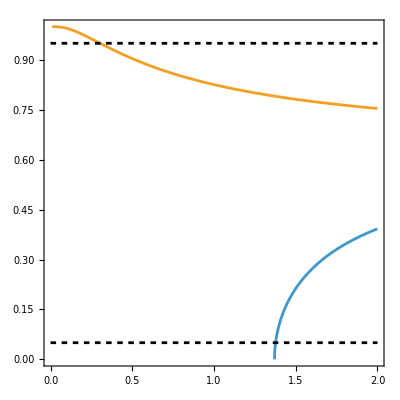

```mathematica
SS=5; 
solX=FullSimplify[x/.Solve[DHC5[x,n,Kp,sn]==z,x]];
maxX=FullSimplify[x/.Solve[D[DHC5[x,n,Kp,sn],x]==0,x][[2]]];
maxHC5=FullSimplify[DHC5[maxX,n,Kp,sn]];
params={Kp->K5,n->SS};
del=0.001;
minSn = sn/.Solve[maxHC5==z,sn][[1]];
vs=Log10[{2,0.5}];
mins={};
Do[
snnow=minSn/.params/.z->vs[[k]];
If[snnow<0.01,AppendTo[mins,0.01],AppendTo[mins,snnow]];
,{k,Length[vs]}];
grs={};
Do[
snnow=mins[[k]];
dHC5s={};
Do[
If[snnow>2.0,Break[]];
intRng=solX/.params/.z->vs[[k]]/.sn->snnow;
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
AppendTo[dHC5s,{snnow,p}];
snnow=snnow+del;
,{t,10000}];
If[Length[dHC5s]>0,AppendTo[grs,dHC5s]];
,{k,Length[vs]}];
ai=ListPlot[grs,Joined->True,AspectRatio->1,Frame->True,PlotRange->{{0,2},{0,1}}];
bi=Plot[0.95,{x,0,2.0},PlotStyle->{Dashing[{0.01,0.01}],GrayLevel[0]}];
ci=Plot[0.05,{x,0,2.0},PlotStyle->{Dashing[{0.01,0.01}],GrayLevel[0]}];
Show[ai,bi,ci]
```

Define a function to calculate the probability for any sn

```mathematica
pCalc05[solX_,params_,maxHC5_,snv_,val_]:=Module[{p},
intRng=solX/.params/.z->Log10[val]/.sn->snv;
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
Return[p];
];
```

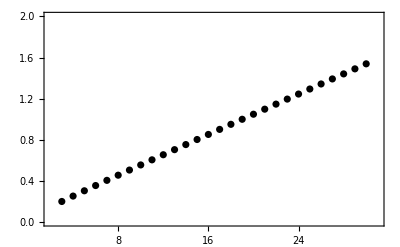

```mathematica
(*Pr[postHC5>1/2 preHC5] = 0.05: Pr[postHC5 < 1/2 preHC5] = 0.95  *)
(*newton method*)
del = 0.0001;
sns={};
Do[
params={Kp->K5,n->k};
snnow =1.;
Do[
FNow = pCalc05[solX,params,maxHC5,snnow,0.5]-0.95;
FAft = pCalc05[solX,params,maxHC5,snnow+del,0.5]-0.95;
If[Abs[FNow]<0.0000001,Break[]];
grad = (FAft-FNow)/del;
snnow = snnow-0.01FNow/grad;
,{t,10000}];
AppendTo[sns,{k,snnow}];
,{k,3,30}];
ListPlot[sns,PlotStyle->{GrayLevel[0]},Frame->True,PlotRange->{{2,31},{0,2}}]
```

Check it is really 0.95

```mathematica
Do[
params={Kp->K5,n->sns[[k]][[1]],sn->sns[[k]][[2]]};
intRng=solX/.params/.z->Log10[0.5];
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
Print["sample size = ",sns[[k]][[1]],", probability = ",p];
,{k,Length[sns]}]
```

sample size = 3, probability = 0.95

sample size = 4, probability = 0.95

sample size = 5, probability = 0.95

sample size = 6, probability = 0.95

sample size = 7, probability = 0.95

sample size = 8, probability = 0.95

sample size = 9, probability = 0.95

sample size = 10, probability = 0.95

sample size = 11, probability = 0.95

sample size = 12, probability = 0.95

sample size = 13, probability = 0.95

sample size = 14, probability = 0.95

sample size = 15, probability = 0.95

sample size = 16, probability = 0.95

sample size = 17, probability = 0.95

sample size = 18, probability = 0.95

sample size = 19, probability = 0.95

sample size = 20, probability = 0.95

sample size = 21, probability = 0.95

sample size = 22, probability = 0.95

sample size = 23, probability = 0.95

sample size = 24, probability = 0.95

sample size = 25, probability = 0.95

sample size = 26, probability = 0.95

sample size = 27, probability = 0.95

sample size = 28, probability = 0.95

sample size = 29, probability = 0.95

sample size = 30, probability = 0.95

## Cadmium toxicity by Van Straalen and Dennneman (1989)

{-0.0132283,0.522444,0.559907,1.13033,1.13988,1.27184,2.18752}

0.971243

0.702761

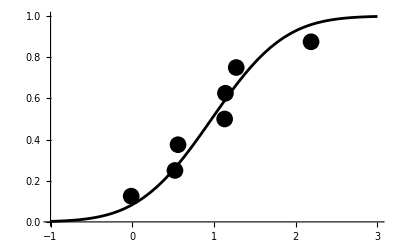

```mathematica
NOECs=Log10[{0.97,3.33,3.63,13.50,13.80,18.70,154.}]
ya=Table[k/8,{k,7}];
m=Mean[NOECs]
sd=StandardDeviation[NOECs]
ai=Plot[CDF[NormalDistribution[m,sd],x],{x,-1,3},PlotStyle->GrayLevel[0],AxesOrigin->{-1,0}];
bi=ListPlot[Transpose[{NOECs,ya}],PlotStyle->{GrayLevel[0],PointSize[0.03]}];
Show[ai,bi]
```

```mathematica
(* Take 3 NOECs from the original datase, and add one*)
```

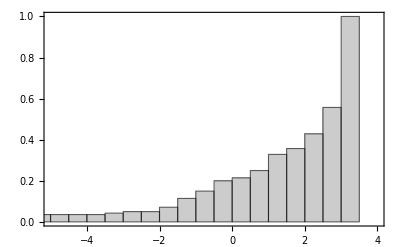

```mathematica
SS=3; 
params={Kp->K5,n->SS,kn->Quantile[NoncentralStudentTDistribution[SS-1,-Sqrt[SS]K5],0.95]/Sqrt[SS],
knn->Quantile[NoncentralStudentTDistribution[SS,-Sqrt[SS+1]K5],0.95]/Sqrt[SS+1]};
dNOECs = {};
Do[
sLst=IntegerDigits[k,2,7];
num=uvec.sLst;
If[num==SS,{
sNOECs={};
nNOECs={};
Do[
If[sLst[[t]]==1,AppendTo[sNOECs,NOECs[[t]]],AppendTo[nNOECs,NOECs[[t]]]];
,{t,7}];

preMean=Mean[sNOECs];
preSD=StandardDeviation[sNOECs];
preNOEC = preMean-(kn/.params)preSD;

Do[
aNOECS=Flatten[{sNOECs,nNOECs[[j]]}];
postMean=Mean[aNOECS];
postSD=StandardDeviation[aNOECS];
postNOEC = postMean-(knn/.params)postSD;
AppendTo[dNOECs,(postNOEC-preNOEC)/preSD];
,{j,7-SS}];
}];
,{k,1,tnum}];
grHist=Histogram[dNOECs,75,"CDF",PlotRange->{{-5,4},{0,1}},AxesOrigin->{-5,0},Frame->True,Frame->True,ChartStyle->GrayLevel[0.8]]
```

3.47558

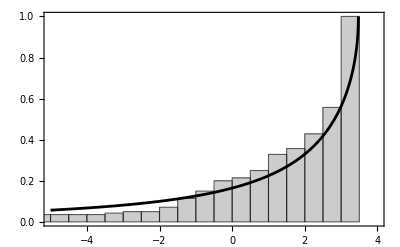

```mathematica
params={Kp->K5,n->SS,sn->1,kn->Quantile[NoncentralStudentTDistribution[SS-1,-Sqrt[SS]K5],0.95]/Sqrt[SS],
knn->Quantile[NoncentralStudentTDistribution[SS,-Sqrt[SS+1]K5],0.95]/Sqrt[SS+1]};
solX=x/.Solve[DPNEC[x,n,Kp,sn,kn,knn]==z,x];
maxX=x/.Simplify[Solve[D[DPNEC[x,n,Kp,sn,kn,knn],x]==0,x][[2]]];
maxPNEC=DPNEC[maxX,n,Kp,sn,kn,knn];
maxZ=maxPNEC/.params
del=0.01;
znow=-5;
myCDF={};
Do[
intRng=solX/.params/.z->znow;
If[znow>maxZ,Break[]];
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
AppendTo[myCDF,{znow,1-p}];
znow=znow+del;
,{k,100000}]
myCDF=AppendTo[myCDF,{maxZ,1}];
grCDF=ListPlot[myCDF,Joined->True,PlotRange->All,AxesOrigin->{-3,0},PlotStyle->GrayLevel[0]];
Show[grHist,grCDF]
```

```mathematica
(* Take 3 NOECs from the original datase, and add one*)
```

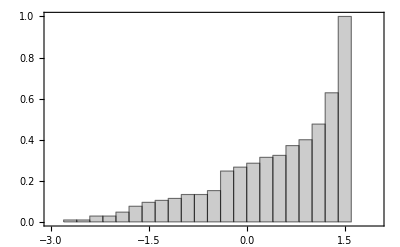

```mathematica
SS=4; 
params={Kp->K5,n->SS,kn->Quantile[NoncentralStudentTDistribution[SS-1,-Sqrt[SS]K5],0.95]/Sqrt[SS],
knn->Quantile[NoncentralStudentTDistribution[SS,-Sqrt[SS+1]K5],0.95]/Sqrt[SS+1]};
dNOECs = {};
Do[
sLst=IntegerDigits[k,2,7];
num=uvec.sLst;
If[num==SS,{
sNOECs={};
nNOECs={};
Do[
If[sLst[[t]]==1,AppendTo[sNOECs,NOECs[[t]]],AppendTo[nNOECs,NOECs[[t]]]];
,{t,7}];

preMean=Mean[sNOECs];
preSD=StandardDeviation[sNOECs];
preNOEC = preMean-(kn/.params)preSD;

Do[
aNOECS=Flatten[{sNOECs,nNOECs[[j]]}];
postMean=Mean[aNOECS];
postSD=StandardDeviation[aNOECS];
postNOEC = postMean-(knn/.params)postSD;
AppendTo[dNOECs,(postNOEC-preNOEC)/preSD];
,{j,7-SS}];
}];
,{k,1,tnum}];
grHist=Histogram[dNOECs,20,"CDF",PlotRange->{{-3,2},{0,1}},AxesOrigin->{-3,0},Frame->True,ChartStyle->GrayLevel[0.8]]
```

1.52522

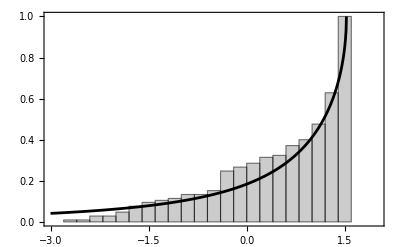

```mathematica
params={Kp->K5,n->SS,sn->1,kn->Quantile[NoncentralStudentTDistribution[SS-1,-Sqrt[SS]K5],0.95]/Sqrt[SS],
knn->Quantile[NoncentralStudentTDistribution[SS,-Sqrt[SS+1]K5],0.95]/Sqrt[SS+1]};
maxZ=maxPNEC/.params
del=0.01;
znow=-3;
myCDF={};
Do[
intRng=solX/.params/.z->znow;
If[znow>maxZ,Break[]];
p=(CDF[StudentTDistribution[SS-1],intRng[[2]]]-CDF[StudentTDistribution[SS-1],intRng[[1]]]);
AppendTo[myCDF,{znow,1-p}];
znow=znow+del;
,{k,100000}]
myCDF=AppendTo[myCDF,{maxZ,1}];
grCDF=ListPlot[myCDF,Joined->True,PlotRange->{{-3,2},{0,1}},PlotStyle->GrayLevel[0],Frame->True];
Show[grHist,grCDF,PlotRange->{{-3,2},{0,1}}]
```